```mathematica
(*3*)
```

```mathematica
(*1.*)
```

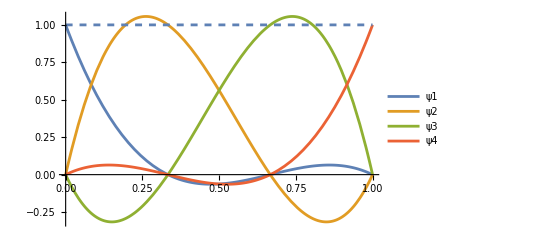

```mathematica
n=3;
Ue[k_] := Sum[Symbol["c"<>ToString[i]]*x^(i-1),{i,1,k+1}];
generateMatrix[N_]:=Table[x[i]^(j-1),{i,N+1},{j,N+1}];
generateCVector[N_]:=Table[Symbol["c"<>ToString[i]],{i,N+1}];
generateUeVector[N_]:=Table[Symbol["U"<>ToString[i]],{i,N+1}];
 M = generateMatrix[n];
Cn= generateCVector[n];
Un = generateUeVector[n];
Csol= LinearSolve[M, Un];
CwithSolution=Thread[Cn->Csol];
UFunc=Coefficient[Collect[Simplify[Sum[Cn[[i]] x^(i-1),{i,n+1}]/. CwithSolution], Un], Un];
CRR[N_]:=Table[x[i]->((i-1))/N,{i,1,N+1}];
result =UFunc/.CRR[n];
fis =Plot[result, {x,0,1}, PlotLegends->{ψ1, ψ2,ψ3,ψ4}];
don = Plot[{y=1},{x, 0,1}, PlotStyle->Dashed];
Show[fis,don]
```

```mathematica
(*2.Lagrangeov Postup*)
```

```mathematica
s=3;
xNodes=Table[Symbol["x"<>ToString[i]],{i,1,s+1}];
uValues=Table[Symbol["U"<>ToString[i]],{i,1,s+1}];
LagrangeBasis[i_,x_]:=Product[(x-xNodes[[j]])/(xNodes[[i]]-xNodes[[j]]),{j,DeleteCases[Range[1,s+1],i]}];
UeSymbolic[x_]:=Sum[uValues[[i]]*LagrangeBasis[i,x],{i,1,s+1}];
UeSimplified=Simplify[UeSymbolic[x]];
xActualNodes=Table[xA+(xB-xA)*(i-1)/s,{i,1,s+1}];
UeWithActualNodes=UeSymbolic[x]/. Thread[xNodes->xActualNodes];
fis =Plot[Evaluate[Table[UeWithActualNodes/. Thread[uValues->UnitVector[s+1,i]],{i,1,s+1}]],{x,0,1}, PlotLegends->{ψ1, ψ2,ψ3,ψ4}];
don = Plot[{y=1},{x, 0,1}, PlotStyle->Dashed];
Show[fis,don]
```

-Graphics-